## A minimal PD example

## Simple BB-PD Element

```mathematica
<<AceGen`;
SMSInitialize["MassSpring","Environment"->"AceFEM","Mode"->"Prototype"];
NMax=100;
SMSTemplate[
"SMSTopology"->"V2"
,"SMSNoNodes"->NMax
,"SMSDOFGlobal"->Table[2,NMax]
,"SMSAdditionalNodes"->Null
,"SMSNodeID"->Join[{"D"},Table["D -D",NMax-1]]
,"SMSNoNodeStorage"->Table[6,NMax]
,"SMSNoElementData"->1
];
```

```mathematica
ComputeNodalForceDensity[]:={
Xi⊢SMSReal[Table[nd$$[1,"X",i],{i,2}]];
Ui⊢SMSReal[Table[nd$$[1,"hp",i],{i,1,2}]];

(*Loop over all j neighbours*)
SMSDo[jNode,2,SMSLastTrueNode[],1,{}];
(*load family member particle data*)
Xj⊢SMSReal[Table[nd$$[jNode,"X",i],{i,2}]];
Uj⊢SMSReal[Table[nd$$[jNode,"hp",i],{i,1,2}]];

(*compute force desity between node i and j*)
ξ⊨Xj-Xi;
η⊨Uj-Ui;
ε⊨(SMSSqrt[(ξ+η).(ξ+η)]-SMSSqrt[ξ.ξ])/SMSSqrt[ξ.ξ];
cs⊨1;
fj⊨cs ε(ξ+η)/SMSSqrt[(ξ+η).(ξ+η)];

(*integrate force density*)
𝒱j⊨.001;
SMSExport[fj 𝒱j,{nd$$[1,"ht",5],nd$$[1,"ht",6]},"AddIn"->True];
SMSEndDo[];
};
```

```mathematica
IntegrateInTime[]:={
Δt⊢SMSReal[rdata$$["TimeIncrement"]];
ρ⊨1;
Xi⊢SMSReal[Table[nd$$[1,"X",i],{i,2}]];
Ui⊢SMSReal[Table[nd$$[1,"hp",i],{i,1,2}]];
Vi⊢SMSReal[Table[nd$$[1,"hp",i],{i,3,4}]];
Li⊢SMSReal[Table[nd$$[1,"hp",i],{i,5,6}]];
L⊢SMSReal[Table[nd$$[1,"ht",i],{i,5,6}]];

U⊨Ui+Δt Vi+Δt^2/(2 ρ)Li;
V⊨Vi+Δt/(2 ρ)(Li+L);
(*Incorporate Exxential BC*)
U⟦1⟧⊨SMSIf[SMSReal[nd$$[1,"DOF",1]]==-1.,SMSReal[nd$$[1,"Bt",1]],U⟦1⟧];
U⟦2⟧⊨SMSIf[SMSReal[nd$$[1,"DOF",2]]==-1.,SMSReal[nd$$[1,"Bt",2]],U⟦2⟧];

SMSExport[U,Table[nd$$[1,"ht",i],{i,1,2}]];
SMSExport[V,Table[nd$$[1,"ht",i],{i,3,4}]];
};
```

```mathematica
SMSStandardModule["Tangent and residual"];
SMSIf[SMSReal[ed$$["Data",1]]<100];
ComputeNodalForceDensity[];
SMSExport[10^6,ed$$["Data",1]];
SMSElse[];
IntegrateInTime[];
SMSExport[1.,ed$$["Data",1]];
SMSEndIf[];

SMSStandardModule["Tasks"];
SMSCharSwitch={"ComputeCurrentForceDensity","IntegrateInTime"};
TaskID⊢SMSInteger[Task$$];
SMSIf[TaskID==-1,SMSExport[{1,0,0,0,0},TasksData$$];SMSReturn[];];
SMSIf[TaskID==-2,SMSExport[{1,0,0,0,0},TasksData$$];SMSReturn[];];

SMSIf[TaskID==1];
ComputeNodalForceDensity[];
SMSEndIf[];

SMSIf[TaskID==2];
IntegrateInTime[];
SMSEndIf[];

SMSWrite[];
```

[0]  Consistency check - expressions

File: MassSpring.c  Size: 15496  Time: 1
Method | SKR | Tasks
No.Formulae | 47 | 53
No.Leafs | 714 | 774

## 2D Example

```mathematica
δ=.3;
XI=Flatten[Table[{x,y},{x,0,10,δ/3},{y,0,10,δ/3}],1];
Elem=Import[NotebookDirectory[]<>"Elem","Table"];
```

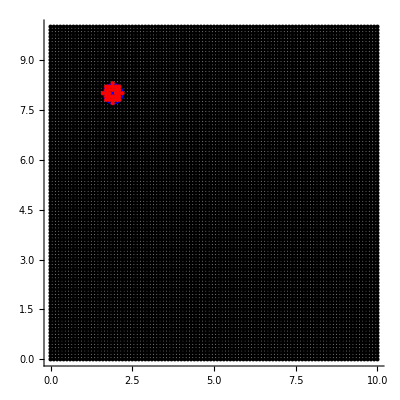

```mathematica
i=2000;
Graphics[{
Point[XI]
,{Blue,Point[XI⟦i⟧],Circle[XI⟦i⟧,δ]}
,{Red,Point[XI⟦Elem⟦i⟧⟦2;;⟧⟧]}
},Axes->True]
```

```mathematica
<<AceFEM`;
SMTInputData[];
SMTAddDomain["Ω","MassSpring",{}];
SMTAddMesh[XI,{"Ω"->Elem}];
SMTAddEssentialBoundary["X"≤δ&,1->0,2->0];
SMTAddEssentialBoundary["X"≥10-δ&,1->.1,2->0];
SMTAnalysis[];
AbsoluteTiming[
Monitor[Do[
SMTNextStep["t"->t,"λ"->t];
SMTTask["ComputeCurrentForceDensity"];
SMTTask["IntegrateInTime"];
progress=ProgressIndicator[t,{0,0.5}];
,{t,0,0.5,10^-3}];,progress]]
```

{9.10161,Null}

```mathematica
TaskSol={SMTNodeData["Y"==5&,"X"]⟦All,1⟧,
SMTNodeData["Y"==5&,"ht"]⟦All,1⟧}ᵀ
Iconize[TaskSol,"Task_Sol"]
```

```mathematica
<<AceFEM`;
SMTInputData[];
SMTAddDomain["Ω","MassSpring",{}];
SMTAddMesh[XI,{"Ω"->Elem}];
SMTAddEssentialBoundary["X"≤δ&,1->0,2->0];
SMTAddEssentialBoundary["X"≥10-δ&,1->.1,2->0];
SMTAnalysis[];
AbsoluteTiming[
Monitor[Do[
SMTNextStep["t"->t,"λ"->t];
SMTNewtonIteration[];
SMTNewtonIteration[];
progress=ProgressIndicator[t,{0,0.5}];
,{t,0,0.5,10^-3}];,progress]]
```

{568.196,Null}

```mathematica
SKRSol={SMTNodeData["Y"==5&,"X"]⟦All,1⟧,
SMTNodeData["Y"==5&,"ht"]⟦All,1⟧}ᵀ;
Iconize[SKRSol,"SKR_Sol"]
```

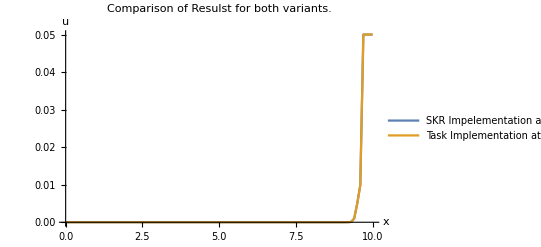

```mathematica
ListLinePlot[
{SKRSol,TaskSol}
,PlotLabel->"Comparison of Resulst for both variants."
,PlotRange->All
,PlotLegends->Placed[{"SKR Impelementation at ~600s","Task Implementation at ~10s"},Scaled[{.5,.8}]]
,AxesLabel->{"x","u"}
]
```